Tutorial: Function Basics
https://reference.wolfram.com/language/ref/Plot.html?q=Plot

```mathematica
x=2
```

2

```mathematica
x+2
```

4

```mathematica
4
```

4

```mathematica
clear[x]
```

clear[2]

```mathematica
f[y_]:=1+2y
```

```mathematica
f[2]
```

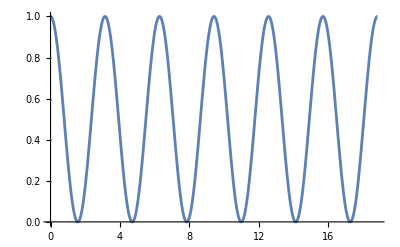

```mathematica
Plot[Sin[x]^2+Cos[2x],{x,0,6 Pi}]
```

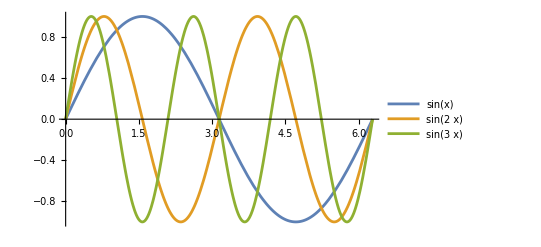

D::ivar: 2 is not a valid variable.

NDSolve::dsvar: 2 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(1,0)[t,2]==0.1 ∂_(2,2) u[t,2],u[0,2]==0,u[t,1]==0.1},u,{t,0,10},{2,0,1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 2 is not a valid variable.

NDSolve::dsvar: 0.000714286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(1,0)[0.000714286,2]==0.1 ∂_(2,2) u[0.000714286,2],u[0,2]==0,u[0.000714286,1]==0.1},u,{0.000714286,0,10},{2,0,1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 2. is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

NDSolve::dsvar: 0.000714286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{u^(1,0)[0.000714286,2.]==0.1 ∂_(2.,2.) u[0.000714286,2.],u[0.,2.]==0.,u[0.000714286,1.]==0.1},u,{0.000714286,0.,10.},{2.,0.,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```